Functions

```mathematica
Basic[data_]:={{"Mean",N@Mean[data]},{"Median",Median[data]},{"Variance",N@Variance[data]},{"Standard Deviation",N@StandardDeviation[data]}}
```

```mathematica
MyCorrelation[data1_,data2_]:=(Total[(data1-Mean[data1])*(data2-Mean[data2])]/(Length[data1]*StandardDeviation[data1]*StandardDeviation[data2]))
```

```mathematica
Contrast
```

```mathematica
image=ImageResize[ColorConvert[-Graphics-,"Grayscale"],{500,500}]
```

-Graphics-

```mathematica
imageData=ImageData[image];
```

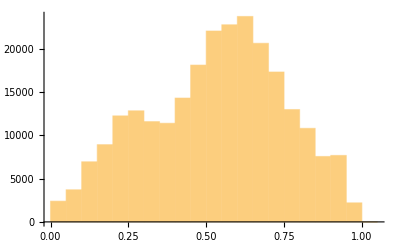

```mathematica
Histogram[Flatten@imageData]
```

```mathematica
Grid[Basic[Flatten@imageData],Frame->All]
```

Mean | 0.52952
Median | 0.552941
Variance | 0.0486296
Standard Deviation | 0.220521

```mathematica
Image[imageData]
```

-Graphics-

```mathematica
Image[2*imageData^2/(1+imageData^2)]
```

-Graphics-

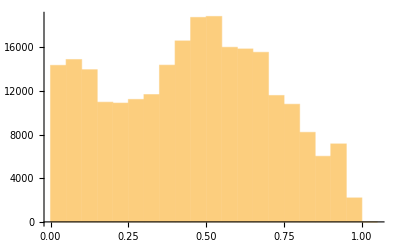

```mathematica
Histogram[Flatten[2*imageData^2/(1+imageData^2),1]]
```

```mathematica
2*imageData^2/(1+imageData^2)
```

```mathematica
Basic[Flatten@imageData]
```

{{Mean,0.52952},{Median,0.552941},{Variance,0.0486296},{Standard Deviation,0.220521}}

```mathematica
Clear[a,b]
```

```mathematica
A={{Mean[Flatten@imageData], 1}, {2*StandardDeviation[Flatten@imageData]+Mean[Flatten@imageData], 1}}
x={{a}, {b}}
B={{.5}, {1}}
```

{{0.52952,1},{0.970562,1}}

{{a},{b}}

{{0.5},{1}}

```mathematica
Solve[Inverse[A].B==x,{a,b}]
```

{{a→1.13368,b→-0.100306}}

```mathematica
MyLine[Data_]:=(Data*1.1336782809644126+-0.10030557230090165)
```

```mathematica
Basic[MyLine[Flatten[imageData]]]
```

{{Mean,0.5},{Median,0.526552},{Variance,0.0625},{Standard Deviation,0.25}}

```mathematica
Image[MyLine[imageData]]
```

-Graphics-

```mathematica
Correlation
```

```mathematica
Clear[a,b]
```

```mathematica
a=Transpose@{Range[1,10],RandomReal[{0,1},10]};
a//MatrixForm
Transpose@a
```

(1 | 0.992919
2 | 0.807631
3 | 0.920106
4 | 0.499368
5 | 0.935718
6 | 0.33179
7 | 0.169339
8 | 0.803014
9 | 0.105334
10 | 0.531252)

{{1,2,3,4,5,6,7,8,9,10},{0.992919,0.807631,0.920106,0.499368,0.935718,0.33179,0.169339,0.803014,0.105334,0.531252}}

```mathematica
o=ConstantArray[{1},Length[a]];
o//MatrixForm
```

(1
1
1
1
1
1
1
1
1
1)

```mathematica
m=o.{Mean[a]};
m//MatrixForm
```

(5.5 | 0.609647
5.5 | 0.609647
5.5 | 0.609647
5.5 | 0.609647
5.5 | 0.609647
5.5 | 0.609647
5.5 | 0.609647
5.5 | 0.609647
5.5 | 0.609647
5.5 | 0.609647)

```mathematica
s=o.{StandardDeviation[a]};
s//MatrixForm
```

(3.02765 | 0.32828
3.02765 | 0.32828
3.02765 | 0.32828
3.02765 | 0.32828
3.02765 | 0.32828
3.02765 | 0.32828
3.02765 | 0.32828
3.02765 | 0.32828
3.02765 | 0.32828
3.02765 | 0.32828)

```mathematica
b=(a-m)/s;
b//MatrixForm
```

(-1.4863 | 1.16752
-1.15601 | 0.603097
-0.825723 | 0.945714
-0.495434 | -0.335929
-0.165145 | 0.993271
0.165145 | -0.846403
0.495434 | -1.34126
0.825723 | 0.589031
1.15601 | -1.53623
1.4863 | -0.238807)

```mathematica
c=(1/Length[a])*Transpose[b].b;
c//MatrixForm
```

(0.9 | -0.565972
-0.565972 | 0.9)

```mathematica
links=Import["http://www.stat.ufl.edu/~winner/datasets.html","Hyperlinks"]
```

```mathematica
ACorrelation[a_]:=(
o=ConstantArray[{1},Length[a]];
m=o.{Mean[a]};
s=o.{StandardDeviation[a]};
b=(a-m)/s;
c=(1/(Length[a]-1))*Transpose[b].b;
c//MatrixForm)
```

```mathematica
ACorrelation[drive]
```

(1. | -0.517844 | 0.9147
-0.517844 | 1. | -0.351953
0.9147 | -0.351953 | 1.)